```mathematica
<<RLBot`;
```

```mathematica
data =  ImportNDJSON["drive_around_field.ndjson", {2}];
```

```mathematica
x = #["car"]["x"] & /@ data;
v = #["car"]["v"] & /@ data;
w = #["car"]["w"] & /@ data;
o = #["car"]["o"] & /@ data;
steer = #["inputs"]["steer"] & /@ data;
```

```mathematica
t
```

```mathematica
ωMax[v_] := steeringCurvature[v] Abs[v]
```

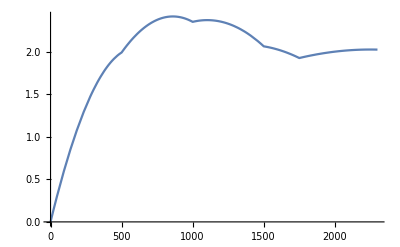

```mathematica
Plot[ωMax[v], {v, 0, 2300}, PlotRange->All]
```

```mathematica
atba[Δx_, v_, ω_] := 5;
```

```mathematica
α[ω_, steer_] := 16.0();
```

```mathematica
throttleAcceleration[1200]
```

365.714

{a1→3.39399,a2→0.235902}

current:18.6565

optimal:9.80609

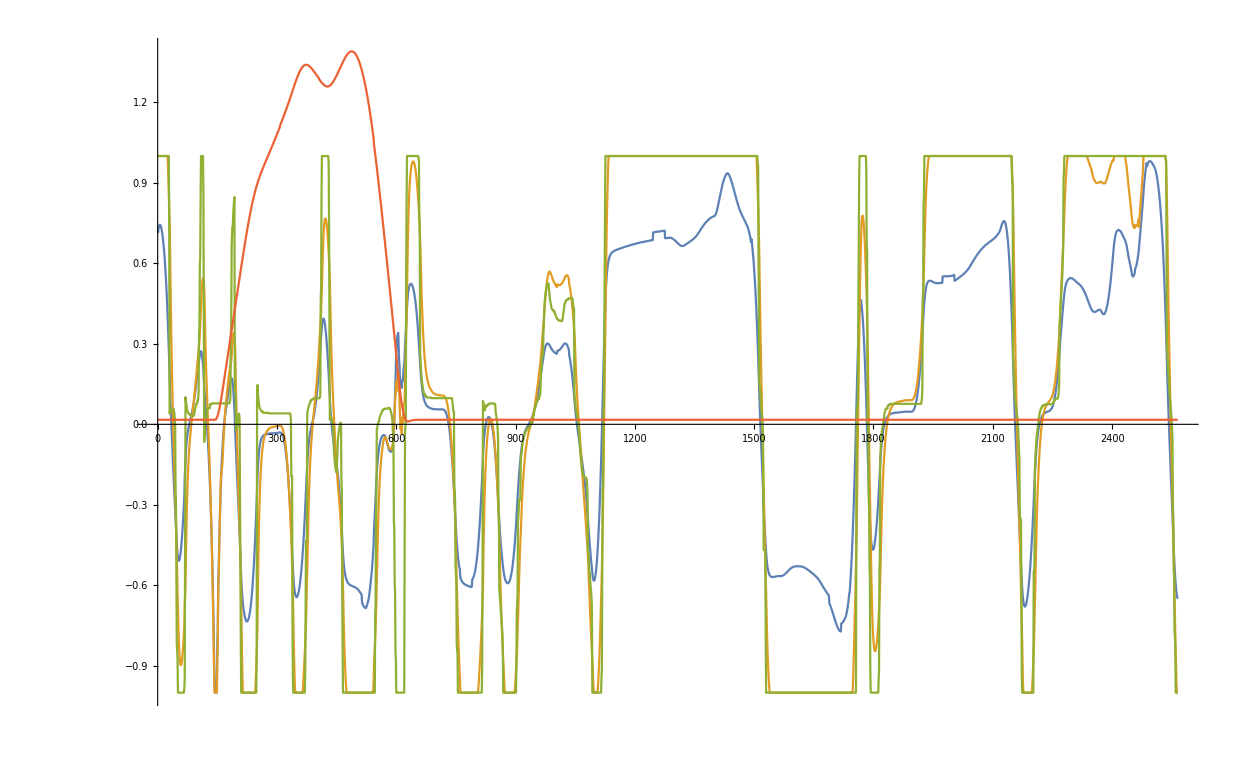

```mathematica
start = 150;
end = Length[x] - 120;
lookahead =30;

data = Table[
ΔxLocal = Transpose[o[[i]]].(x[[i + lookahead]] - x[[i]]);
ωLocal = (Transpose[o[[i]]].(w[[i]]))[[3]];
ϕ = ArcTan[ΔxLocal[[1]], ΔxLocal[[2]]];
{ϕ, ωLocal,steer[[i]]}
,
{i, start, end}
];

model[z1_, z2_] := Clip[a1 z1 + a2 z2 , {-1, 1}]
rule = FindFit[data, model[z1, z2], {a1, a2}, {z1, z2}]

actual = data[[All, -1]];

current = (model[#[[1]], #[[2]]] /.  {a1->3, a2->0}) & /@ data;
Print["current:"<>ToString[Norm[current - actual]]]

predicted = (model[#[[1]], #[[2]]] /. rule) & /@ data;
Print["optimal:"<>ToString[Norm[predicted - actual]]]

Show[
ListLinePlot[{current, predicted, actual, x[[start;;end, 3]]/1000}]
]
```